```mathematica
(*for mu=(nn+1)wc*)
mmp={{1,-6/1000000},{2,-0.00008},{3,-0.000378},{4,-0.001152},{5,-0.00275},{6,-0.005616},{7,-0.01029},{8,-0.017408},{9,-0.027702},{10,-0.042},{11,-0.061226},{15,-0.20925},{20,-0.656},{25,-1.59375},{36,-6.81179}}
```

{{1,-3/500000},{2,-0.00008},{3,-0.000378},{4,-0.001152},{5,-0.00275},{6,-0.005616},{7,-0.01029},{8,-0.017408},{9,-0.027702},{10,-0.042},{11,-0.061226},{15,-0.20925},{20,-0.656},{25,-1.59375},{36,-6.81179}}

```mathematica
(*for mu=(nn+5/4)wc*)
mmp={{1,-0.000011718749999995204},{2,-0.00011390625000001512},{3,-0.00048059375000001367},{4,-0.0013817812499997868 },{5,-0.0031834687499965124},{6,-0.006347656250000673},{7,-0.011432343750003918},{8,-0.019091531250061876},{9,-0.030075218750580925},{10,-0.045229406255425444},{15,-0.21988784346965443 },{20,-0.680908781225506},{25,-1.6420422187157102}}
```

{{1,-0.0000117187},{2,-0.000113906},{3,-0.000480594},{4,-0.00138178},{5,-0.00318347},{6,-0.00634766},{7,-0.0114323},{8,-0.0190915},{9,-0.0300752},{10,-0.0452294},{15,-0.219888},{20,-0.680909},{25,-1.64204}}

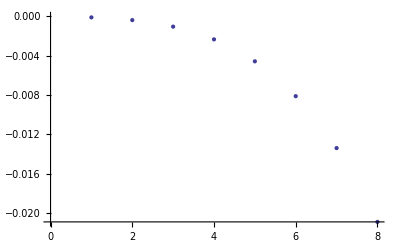

```mathematica
ListPlot[mmp]
```

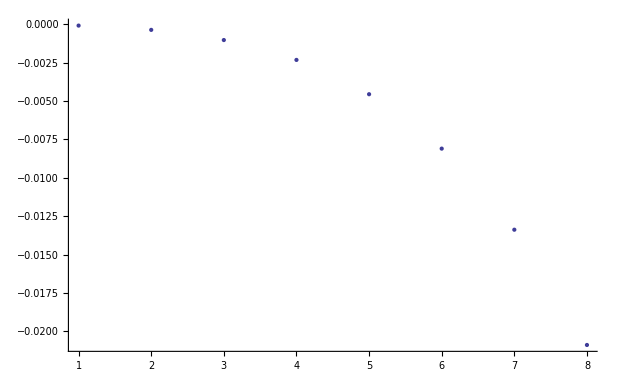

```mathematica
ListPlot[mmp,PlotRange->{{0,37},{0,-7}}]
```

```mathematica
mmpline=Fit[mmp,{x^4},x]
```

-4.21331×10^-6 x^4

```mathematica
mmpline/.x->35
```

-6.12829

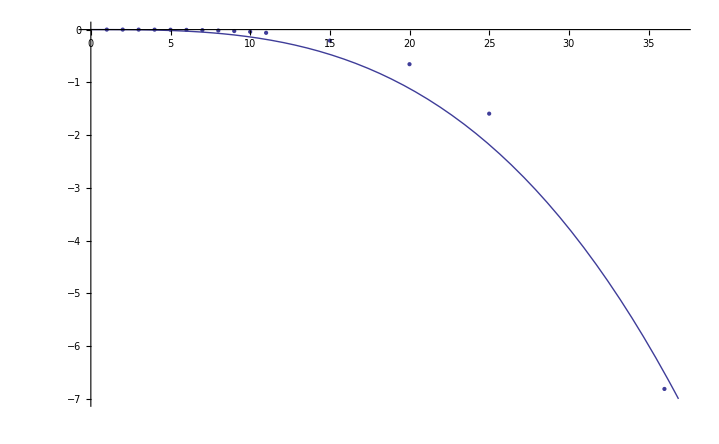

```mathematica
Show[Plot[mmpline,{x,0,37},PlotRange->{{0,37},{0,-7}}],ListPlot[mmp]]
```

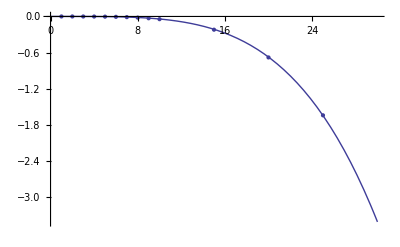

```mathematica
Show[Plot[mmpline,{x,0,30},PlotRange->Automatic],ListPlot[mmp]]
```